# Mappa logistica

Cammelli Tonanti, ovvero Riccardo Cazzin e Francesco Tognetti

Università degli Studi di Padova

Le iterazioni della mappa logistica f_μ=μx(1-x), che dipende dal parametro positivo μ, costituiscono (a prima vista) una versione discreta della dinamica continua descritta dall’equazione logistica. A differenza di quest’ultima, però, la dinamica discreta della mappa logistica è enormemente complicata.

## Lemmi introduttivi e visualizzazione delle orbite.

Con mappa logistica intendiamo la funzione polinomiale reale f_μ(x)=μ x (1-x), con μ>0. Ci occuperemo soprattutto delle iterazioni di f_μ, ossia delle funzioni f_μ^n=f_μ∘…∘f_μ: studieremo, al variare del parametro μ, il comportamento delle orbite generate da f_μ, ovvero degli insiemi del tipo {x_0,f_μ(x_0),f_μ^2(x_0),…}; in particolare, vedremo sotto quali ipotesi tali orbite posseggano uno o più attrattori. In seguito, mostreremo un’applicazione, resasi assai attuale nell’ultimo periodo, che modellizza l’andamento di un’epidemia proprio con la mappa f_μ.

```mathematica
(*Evitiamo di entrare in conflitto con altri progetti aperti.*)
ClearAll["Global`*"] 

(*Definiamo Subscript[f, μ]. Definiamo subito anche l'iterata di Subscript[f, μ], dato che la useremo molto spesso.*)
f[μ_,x_]:=μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n] 
fnList[μ_,x_,n_]:=NestList[f[μ,#]&,x,n]
```

Applicando in modo iterato la mappa logistica a partire da un punto iniziale x_0∈ℝ, ci chiediamo se la mappa ammetta un punto fisso, ovvero un x_f_μ∈ℝ tale che f_μ(x_f_μ)=x_f_μ.

Lemma 1. Per ogni μ>0, f_μ ha come unici punti fissi 0 e 1-1/μ.

Dimostrazione. Si può lasciare a Mathematica la soluzione dell’equazione di punto fisso: si applica First per rimuovere le espressioni condizionali, dato che il caso μ=1 dà come unico punto fisso con molteplicità doppia il punto x=0. I punti trovati sono quelli richiesti dal Lemma.

```mathematica
First/@(x/.Solve[{μ>0,f[μ,x]==x},x,Reals])
```

□

A priori la mappa logistica potrebbe essere studiata su tutto ℝ. Coi prossimi lemmi, invece, mostriamo che lo studio più fecondo avviene nell’intervallo [0,1].

Lemma 2. Per ogni μ>1, se x_0>1 oppure x_0<0, allora f_μ^n(x_0)→-∞.

Dimostrazione. Mostriamo innanzitutto per quali x∈ℝ si abbia f_μ(x)<x. Se risulta che, chiamato U il sottoinsieme di ℝ che verifichi la disuguaglianza sopra, a tale U appartengono sia f_μ(x_0) sia x_0 per ogni x_0>1 e per ogni x_0<0, allora f_μ^n(x_0) è una successione monotona decrescente inferiormente illimitata, e si è provata la tesi.

```mathematica
Reduce[{μ>1,f[μ,x]<x},x,Reals]
```

È evidente, poi, che f_μ(x_0)<0 per ogni x_0>1>1-1/μ e per ogni x_0<0, dunque la successione f_μ^n(x_0) diverge a -∞ in questi due casi.

□

Lemma 3. Se x_0<0 oppure x_0>1, allora esiste 0<μ≤1 tale che f_μ^n(x_0)→-∞.

Dimostrazione. Usiamo un approccio analogo a quello del Lemma 2:

```mathematica
Reduce[{0<μ≤1,f[μ,x]<x},x,Reals]
```

Trattiamo innanzitutto il caso x_0>1:

```mathematica
Reduce[{0<μ≤1,x0>1,f[μ,x0]<(-1+μ)/μ},x0,Reals]
```

Scegliendo 1>μ>1/x_0>0 si ottiene quanto richiesto. Trattiamo ora il caso x_0<0: poiché è sufficiente che x_0<1-1/μ, basta scegliere 1>μ>1/(1-x_0)>0.

□

Col prossimo lemma, infine, restringiamo l’intervallo dei μ che intendiamo prendere in considerazione.

Lemma 4. Se 0<μ≤4, allora tutte le orbite con dato iniziale in [0,1] rimangono in tale intervallo. Se, invece, μ>4, allora esiste un intervallo A_0⊆[0,1] tale che ogni orbita con dato iniziale in A_0 non è contenuta in [0,1] a partire dalla prima iterazione.

Dimostrazione. La prova del Lemma 4 è immediata, se si considerano le seguenti disuguaglianze:

```mathematica
Reduce[{0≤x≤1,0≤f[μ,x]≤1,0<μ≤4},x]
Reduce[{0≤x≤1,0≤f[μ,x]≤1,μ>4},x]
```

□

Alla luce di questo risultato, decidiamo di studiare la dinamica della mappa logistica per μ<4.

Dopo aver delimitato quanto più possibile gli intervalli da studiare, osserviamo come può evolvere un'orbita al variare di μ e x_0.

```mathematica
graficoOrbita[μ_,x_,n_]:=With[
{
(*Precalcoliamo l'orbita, disposta sulla bisettrice.*)
pts=Table[{ξ,ξ},{ξ,fnList[μ,x,n]}]
},
(*Disegniamo la parabola Subscript[f, μ] e la bisettrice del I e del III quadrante; mostriamo poi l'orbita tenendo traccia dell'ultimo punto (in azzurro).*)
Plot[
{f[μ,t],t},
{t,Min[x,0],Max[x,1]},

]]
```

```mathematica
Manipulate[graficoOrbita[μ,x0,n],{{μ,1.2},0,4},{{x0,0.4},0,1},{{n,21},Range[1,201,10]}]
```

## Biforcazioni e caos

Grazie al grafico dinamico sopra, si può notare che per 0<μ≤1 tutte le orbite tendono a 0, unico punto fisso in [0,1] per tali μ. Ciò è dovuto al fatto che, con 0<μ≤1, si ha f_μ(x)≤x per ogni x∈[0,1], ma al contempo f_μ(x)≥0 per tali x in base al Lemma 4: per il teorema sul limite di successioni monotone, qualunque orbita con dato iniziale in [0,1] ammette limite e tale limite è proprio 0. La situazione cambia se μ>1.

Lemma 5. Per ogni μ>1 il punto 0 è un punto fisso repulsivo di f_μ.

Dimostrazione. Un punto fisso x_0 è repulsivo per f_μ se e solo se |f'_μ(x_0)|>1. Dal momento che f'_μ(0)=μ>1, la tesi è verificata.

```mathematica
D[f[μ,x],x]/.x->0
```

□

Per μ>1 il punto fisso x_μ=1-1/μ appartiene a [0,1] e, dunque, può essere preso in considerazione.

Lemma 6.  Il punto fisso x_μ=1-1/μ per f_μ è attrattivo per 1<μ<3 e repulsivo per μ>3.

Dimostrazione. Con un ragionamento simile a quello usato nel Lemma 5, calcoliamo la derivata di f_μ in x_μ:

```mathematica
Simplify[D[f[μ,x],x]/.x->1-1/μ]
```

Dato che |2-μ|<1 per 1<μ<3 e |2-μ|>1 per μ>3, si è provata la tesi.

□

Nel caso 1<μ≤3, dunque, le orbite di tutti gli x∈(0,1) convergono a x_μ e le orbite di 0 e 1 convergono a 0. Come si può notare a livello grafico, però, la convergenza verso x_μ diviene sempre più lenta man mano che μ si avvicina a 3 e, superatolo, essa scompare per lasciare il posto ad orbite di periodo 2.

Lemma 7. L’orbita di periodo minimo 2 di f_μ esiste per μ>3 ed è attrattiva per 3<μ<1+√6.

Dimostrazione. Se un’orbita per f_μ ha come periodo minimo 2, allora i due punti attrattivi x_1 e x_2 sono punti fissi di f_μ^2. Calcoliamo, dunque, i punti fissi di f_μ^2

```mathematica
Solve[{fn[μ,x,2]==x,μ>0,0≤x≤1},x,Reals]
```

Confrontando i quattro risultati ottenuti con i punti fissi di f_μ, spostiamo l’attenzione sugli ultimi due risultati, che valgono per μ>3. Calcoliamo la derivata di f_μ^2 nei punti fissi appena trovati:

```mathematica
Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

e vediamo per quali μ>3 sono punti attrattivi.

```mathematica
Reduce[RealAbs[#]<1&&μ>3,μ,Reals]&/@Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

Ciò conferma quanto affermato nella tesi.

□

Ogni nuova biforcazione è prodotta dallo stesso fenomeno analitico. Alla n-esima biforcazione, infatti, le orbite attrattive convergono ai punti fissi di f_μ^(2^n) che abbiano modulo della derivata strettamente minore di 1: posseggono questa caratteristica i punti fissi di f_μ^(2^n) che non sono anche punti fissi di f_μ^(2^(n-1)). Tali punti attrattivi compaiono non appena i punti fissi di f_μ^(2^n) che sono anche punti fissi di f_μ^(2^(n-1)) hanno derivata di modulo maggiore di 1; come si vede nel grafico sotto, infatti, la comparsa di nuovi attrattori è strettamente collegata al superamento della soglia 1 per il modulo della derivata calcolata negli attrattori “precedenti” — e questa crescita del modulo della derivata si ottiene con l’aumentare di μ.

```mathematica
Manipulate[
GraphicsRow[
{
Plot[{fn[μ,x,n],x},{x,0,1},
,
Epilog->{Red,Point[{x,x}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
],
Plot[{Abs[D[fn[μ,y,n],y]]/.y->x,1},{x,0,1},
,
Epilog->{Red,Point[{x,Abs[D[fn[μ,y,n],y]/.y->x]}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
]
}
],
{μ,3,3.57},
{n,2^Range[3]}
]
```

Dopo aver capito il motivo per il quale i punti perdono di attrattività dopo aver passato un certo μ, si può tracciare un grafico dei punti fissi e delle prime orbite attrattive al variare di μ:

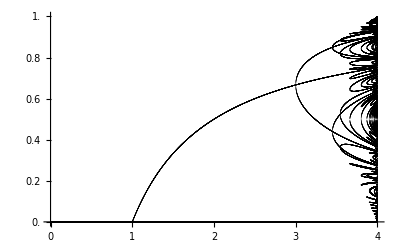

```mathematica
ListPlot[
Union@Flatten[
Table[
ParallelTable[{μ,x}/.NSolve[{fn[μ,x,n]==x,x≥0},x,Reals],{μ,Subdivide[0,4,10^4]}],
{n,2^Range[0,3]}
],
2
],

]
```

Non vanno considerate in questo grafico le orbite non generate direttamente dalla biforcazione.